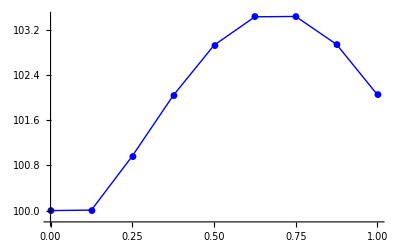

Forward Euler for population growth

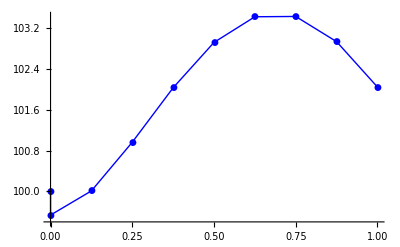

Runge-Kutta with p=4 for population growth

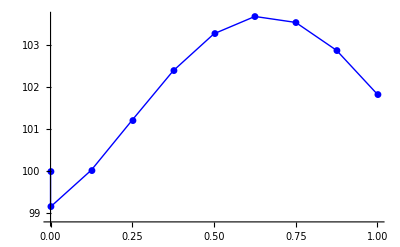

Runge-Kutta with p=5 for population growth

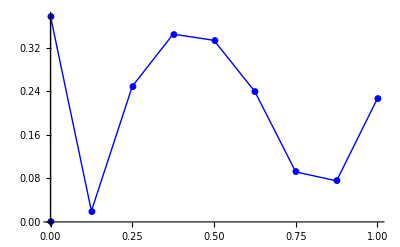

Runge-Kutta error at each time step with p=5 and p=4

```mathematica
Clear[t, y, Δt,i,Np,B,rkArray,rk2Array]
B[t_]:=.00713535-.03774882*t+.06101010*t^2-.02473805*t^3;

Δt=.125;

Np[t_,y_]:=.09*y-B[t]*y^1.7;
i=0;
Subscript[t, i]=0;
Subscript[y, i]=100.;
feArray={{Subscript[t, i],Subscript[y, i]}};
While[i<9,
	Subscript[k, 0]=Np[Subscript[t, i],Subscript[y, i]];
	Subscript[y, i+1]=Subscript[y, i]+(Subscript[k, 0])*Δt;
	i++;
	Subscript[t, i]=Subscript[t, i-1]+Δt;
	AppendTo[feArray,{Subscript[t, i],Subscript[y, i+1]}];
]
fePlot=ListLinePlot[feArray, PlotMarkers->Automatic,PlotStyle->{Blue}];
Show[fePlot]
Print["Forward Euler for population growth"]
t=0;
i=0;
Subscript[y, i]=100;
rkArray={{t,Subscript[y, i]}};
rk2Array={{t,Subscript[y, i]}};
eArray={{t,0}};
While[i<9,
Subscript[k, 0]=Δt*Np[t,Subscript[y, i]];
Subscript[k, 1]=Δt*Np[t+.25*Δt,Subscript[y, i]+.25*Subscript[k, 0]];
Subscript[k, 2]=Δt*Np[t+3./8.*Δt,Subscript[y, i]+3./32.*Subscript[k, 0]+9./32. Subscript[k, 1]];
Subscript[k, 3]=Δt*Np[t+12./13. Δt,Subscript[y, i]+1932./2197.*Subscript[k, 0]-7200./2197.*Subscript[k, 1]+7296./2197.*Subscript[k, 2]];
Subscript[k, 4]=Δt*Np[t+Δt,Subscript[y, i]+439./216.*Subscript[k, 0]-8*Subscript[k, 1]+3680./513.*Subscript[k, 2]-845./4104.*Subscript[k, 3]];
Subscript[k, 5]=Δt*Np[t+.5*Δt,Subscript[y, i]-8./27.*Subscript[k, 0]+2 Subscript[k, 1]-3544./2565.*Subscript[k, 2]*1859./4104.*Subscript[k, 3]-11./40.*Subscript[k, 4]];
Subscript[y, i+1]=Subscript[y, i]+25./216.*Subscript[k, 0]+1408./2565.*Subscript[k, 2]+2197./4014.*Subscript[k, 3]-1./5.*Subscript[k, 4];
Subscript[y, bar2]=Subscript[y, i]+16./35.*Subscript[k, 0]+6656./12825.*Subscript[k, 2]+28561./56430.*Subscript[k, 3]-9./50.*Subscript[k, 4]+2./55.*Subscript[k, 5];
AppendTo[rkArray,{t,Subscript[y, i+1]}];
AppendTo[rk2Array, {t,Subscript[y, bar2]}];
AppendTo[eArray,{t,Abs[Subscript[y, bar2]-Subscript[y, i+1]]}];
i++;
t=t+Δt;
]
rkPlot=ListLinePlot[rkArray, PlotMarkers->Automatic,PlotStyle->{Blue}];
Show[rkPlot]
Print["Runge-Kutta with p=4 for population growth"]
rk2Plot=ListLinePlot[rk2Array, PlotMarkers->Automatic,PlotStyle->{Blue}];
Show[rk2Plot]
Print["Runge-Kutta with p=5 for population growth"]
ePlot=ListLinePlot[eArray, PlotMarkers->Automatic,PlotStyle->{Blue}];
Show[ePlot]
Print["Runge-Kutta error at each time step with p=5 and p=4"]
```